# Computational explorations in modern number theory : the Green–Tao theorem and the abc conjecture

## Ryukyu Chihara University of the Ryukyus Okinawa Island, Japan

### Green - Tao Theorem

```mathematica
(*Define initial terms*)
initialTerms={1,3,7,9};

(*Parameters*)
maxC=1000;
maxB=500;
length=8;

(*Check arithmetic progression of primes*)
Do[Do[Do[terms=Table[a+10*b+10*(k-1)*c,{k,1,length}];
If[AllTrue[terms,PrimeQ],Print[terms]],{c,1,maxC}],{b,0,maxB}],{a,initialTerms}]
```

{61,9931,19801,29671,39541,49411,59281,69151}

{521,10181,19841,29501,39161,48821,58481,68141}

{541,9151,17761,26371,34981,43591,52201,60811}

{881,1091,1301,1511,1721,1931,2141,2351}

{1091,3821,6551,9281,12011,14741,17471,20201}

{1531,6151,10771,15391,20011,24631,29251,33871}

{4091,12071,20051,28031,36011,43991,51971,59951}

{4721,7451,10181,12911,15641,18371,21101,23831}

{73,5953,11833,17713,23593,29473,35353,41233}

{103,4723,9343,13963,18583,23203,27823,32443}

{433,3583,6733,9883,13033,16183,19333,22483}

{1063,7573,14083,20593,27103,33613,40123,46633}

{2063,3323,4583,5843,7103,8363,9623,10883}

{2693,4583,6473,8363,10253,12143,14033,15923}

{3083,7703,12323,16943,21563,26183,30803,35423}

{3323,4583,5843,7103,8363,9623,10883,12143}

{3413,8663,13913,19163,24413,29663,34913,40163}

{3583,6733,9883,13033,16183,19333,22483,25633}

{3593,11783,19973,28163,36353,44543,52733,60923}

{3823,6133,8443,10753,13063,15373,17683,19993}

{17,6947,13877,20807,27737,34667,41597,48527}

{137,8117,16097,24077,32057,40037,48017,55997}

{937,10177,19417,28657,37897,47137,56377,65617}

{1637,2267,2897,3527,4157,4787,5417,6047}

{1847,3947,6047,8147,10247,12347,14447,16547}

{1867,10477,19087,27697,36307,44917,53527,62137}

{3167,9887,16607,23327,30047,36767,43487,50207}

{3257,7877,12497,17117,21737,26357,30977,35597}

{3347,10487,17627,24767,31907,39047,46187,53327}

{3907,8737,13567,18397,23227,28057,32887,37717}

{199,409,619,829,1039,1249,1459,1669}

{199,9439,18679,27919,37159,46399,55639,64879}

{409,619,829,1039,1249,1459,1669,1879}

{619,829,1039,1249,1459,1669,1879,2089}

{1019,3329,5639,7949,10259,12569,14879,17189}

{1289,2969,4649,6329,8009,9689,11369,13049}

{1559,7019,12479,17939,23399,28859,34319,39779}

{1609,11059,20509,29959,39409,48859,58309,67759}

{1699,5689,9679,13669,17659,21649,25639,29629}

{2239,2659,3079,3499,3919,4339,4759,5179}

{2909,6899,10889,14879,18869,22859,26849,30839}

{3449,13109,22769,32429,42089,51749,61409,71069}

{3499,3709,3919,4129,4339,4549,4759,4969}

{3709,3919,4129,4339,4549,4759,4969,5179}

## The abc conjecture

```mathematica
(* Define the radical *)
Rad[n_]:=Times@@Cases[FactorInteger[n],{x_,_}->x];
```

```mathematica
(* kappa*)
κ=1.4;
```

```mathematica
(* Examples of c ≥ rad(abc)^κ *)
Do[Do[If[GCD[a,b,a+b]==1&&a+b≥Rad[a*b*(a+b)]^κ,
Print["a=",a,",","b=",b,",","c=",a+b],Null],
{b,a+1,a+10000}],{a,1,1000}]
```

a=1,b=2400,c=2401

a=1,b=4374,c=4375

a=3,b=125,c=128

## The Collatz conjecture

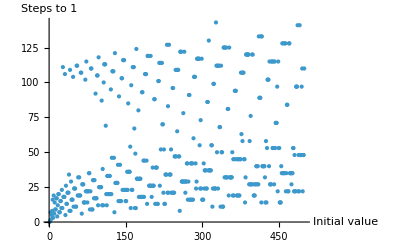

```mathematica
(* computing the stopping step for the Collatz sequence with the initial data m=1,...,500*)
collatz[n_]:=If[EvenQ[n],n/2,3 n+1]

stoppingTime[m_]:=Length[NestWhileList[collatz,m,#>1&]]-1

ListPlot[Table[{m,stoppingTime[m]},{m,1,500}],PlotStyle->PointSize[Small],AxesLabel->{"Initial value","Steps to 1"}]
```